```mathematica
SystemOpen@FileNameJoin[{$UserBaseDirectory,"Applications"}]
```

```mathematica
updateMaTeX[]:=Module[{json,download,target},Check[json=Import["https://api.github.com/repos/szhorvat/MaTeX/releases/latest","JSON"];
download=Lookup[First@Lookup[json,"assets"],"browser_download_url"];
target=FileNameJoin[{CreateDirectory[],"MaTeX.paclet"}];
If[$Notebooks,PrintTemporary@Labeled[ProgressIndicator[Appearance->"Necklace"],"Downloading...",Right],Print["Downloading..."]];
URLSave[download,target],Return[$Failed]];
If[FileExistsQ[target],PacletManager`PacletInstall[target],$Failed]]
```

```mathematica
Needs["PacletManager`"]
PacletInstall["~/Downloads/MaTeX-1.7.10.paclet"]
```

PacletInstall::samevers: A paclet named MaTeX with the same version number (1.7.10) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with IgnoreVersion->True.

$Failed

$Failed

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\input{/home/waltera/A/preambuloInkscape.tex}"}];
Quiet[MaTeX["\\pec{x}", Magnification->1.5]];
ClearMaTeXCache[];
```

```mathematica
{MaTeX["\\pec{x}", Magnification->1.5],MaTeX["\\pec{y}", Magnification->1.5],MaTeX["\\pec{z}", Magnification->1.5]}
```

MaTeX::texerr: Error while running LaTeX.

MaTeX::stderr: Additional error information received:
kpathsea: Running mktexfmt pdflatex.fmt
mktexfmt: No such file or directory

MaTeX::texerr: Error while running LaTeX.

MaTeX::stderr: Additional error information received:
kpathsea: Running mktexfmt pdflatex.fmt
mktexfmt: No such file or directory

MaTeX::texerr: Error while running LaTeX.

General::stop: Further output of MaTeX::texerr will be suppressed during this calculation.

MaTeX::stderr: Additional error information received:
kpathsea: Running mktexfmt pdflatex.fmt
mktexfmt: No such file or directory

General::stop: Further output of MaTeX::stderr will be suppressed during this calculation.

{$Failed,$Failed,$Failed}

```mathematica
Ejes3DT[xmin_,xmax_,ymin_,ymax_,zmin_,zmax_,plano_: " ", txt_:True, grosor_:0.005, p_:1.5]:={
Gray,Arrowheads[p/100*Max[{xmax,ymax,zmax}]],
Arrow[Tube[{{xmin,0,0.01},{0,0,0.01},{xmax,0,0.01}}, grosor]   ],
Arrow[Tube[{{0,ymin+0.01,0.01},{0,0,0.01},{0,ymax+0.01,0.01}}, grosor]],
Arrow[Tube[{{0.01,0.01,zmin+0.01},{0.01,0.01,0.01},{0,0,zmax+0.01}}, grosor]],
LightGray,
Which[
plano==" ",{ Point[{0,0,0}]  },
plano=="xy",
{Table[Line[{{IntegerPart[xmin],i,0},{IntegerPart[xmax],i,0}}],{i,IntegerPart[ymin],IntegerPart[ymax],1}],Table[Line[{{i,IntegerPart[ymin],0},{i,IntegerPart[ymax],0}}],{i,IntegerPart[xmin],IntegerPart[xmax],1}]},
plano=="xz",
{Table[Line[{{IntegerPart[xmin],0,i},{IntegerPart[xmax],0,i}}],{i,IntegerPart[zmin],IntegerPart[zmax],1}],
Table[Line[{{i,0,IntegerPart[zmin]},{i,0,IntegerPart[zmax]}}],{i,IntegerPart[xmin],IntegerPart[xmax],1}]},
plano=="yz",
{Table[Line[{{0,i,IntegerPart[zmin]},{0,i,IntegerPart[zmax]}}],{i,IntegerPart[ymin],IntegerPart[ymax],1}],
Table[Line[{{0,IntegerPart[ymin],i},{0,IntegerPart[ymax],i}}],{i,IntegerPart[zmin],IntegerPart[zmax],1}]}
],
If[txt,{Text[-Graphics-,1.1{xmax,0,0.1}],Text[-Graphics-,1.1{0,ymax,0}],Text[-Graphics-,{0,0.3,zmax-0.1}]}]
};

azul=RGBColor[23/255,7/255,142/255];
verde=RGBColor[0, 0.666667, 0];
magenta=RGBColor[1, 0, 1];
rojo=RGBColor[1,25/255,144/255];
naranja=RGBColor[1, 0.333333, 0];
gris=RGBColor[14/255,14/255,14/255];
celeste=RGBColor[2 /255,99/255,176/255];

CompleteTheSquare::notquad="The expression is not quadratic in the variables `1`";
CompleteTheSquare[expr_]:=CompleteTheSquare[expr,Variables[expr]]
CompleteTheSquare[expr_,Vars_Symbol]:=CompleteTheSquare[expr,{Vars}]
CompleteTheSquare[expr_,Vars:{__Symbol}]:=Module[{array,A,B,C,s,vars,sVars},vars=Intersection[Vars,Variables[expr]];
Check[array=CoefficientArrays[expr,vars],Return[expr],CoefficientArrays::poly];
If[Length[array]≠3,Message[CompleteTheSquare::notquad,vars];Return[expr]];
{C,B,A}=array;A=Symmetrize[A];
s=Simplify[1/2 Inverse[A].B,Trig->False];
sVars=Hold/@(vars+s);A=Map[Hold,A,{2}];
Expand[A.sVars.sVars]+Simplify[C-s.A.s,Trig->False]//ReleaseHold];

Ejes2DM[a1_,b1_,a2_,b2_,garr_:0.03, color_:Gray]:=Module[{factor},factor=35*garr;
{
color,AbsoluteThickness[1],Arrowheads[factor/20],
Arrow[{{a1{1,0}, b1{1,0}}}],Arrow[{{a2{0,1}, b2{0,1}}}],
Text[MaTeX["\\pec{x}", Magnification->factor],{b1-0.1,-0.3}],
Text[MaTeX["\\pec{y}", Magnification->factor],{0.3,b2-0.2}]}
]

or={0,0}
```

{0,0}

```mathematica
0.04*50
```

2.

## Figuras

```mathematica
A={1,1}; B={2,4}; c={4,0}; P={3,1};
Graphics[{
Thickness[0.08], AbsolutePointSize[7], 
Line[{A,B,c,A}],
RGBColor[0.929412, 0.92549, 0.92549],Polygon[{A,B,c}],
Black, Point[{A,B,c}], Magenta ,Point[P]

}, ImageSize->50]
```

-Graphics-

## Intervalos

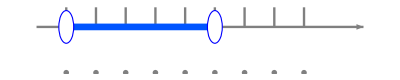

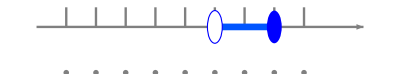

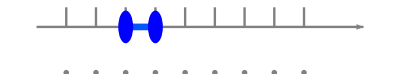

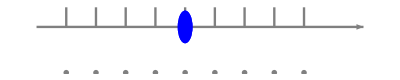

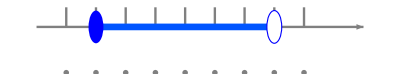

```mathematica
intervaloG[a1_,b1_,paso_:1,tca_,aa_,bb_,tcb_,r_:0.1]:=
Graphics[{
AbsoluteThickness[1.7], Gray, Arrowheads[0.08],
Arrow[{{{a1-1,0}, {b1+2,0}}}],
Table[{Line[{{t,0},{t,0.3}}]},{t,a1,b1,paso}],
Table[Text[MaTeX[t, Magnification->1.1],{t,-0.7}],{t,a1,b1,paso}],
RGBColor[0, 0.333333, 1],Thickness[0.012],Line[{{aa,0},{bb,0}}],
Which[tca=="[",{Blue,Disk[{aa,0},r]},tca=="]",{EdgeForm[Directive[Thick,Blue]],White,Disk[{aa,0},r]}],
Which[tcb=="]", {Blue,Disk[{bb,0},r]},tcb=="[",{EdgeForm[Directive[Thick,Blue]],White,Disk[{bb,0},r]}]
}, ImageSize->400];

intervaloG[-2,6,1, "]",-2,3,"[",0.25]
intervaloG[0,8,1, "]",5,7,"]",0.25]
intervaloG[0,8,1, "[",2,3,"]",0.25]
intervaloG[0,8,1, "[",4,4,"]",0.25]
intervaloG[0,8,1, "[",1,7,"[",0.25]
```

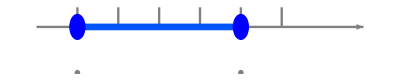

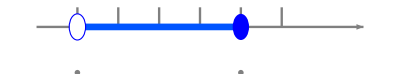

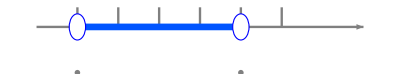

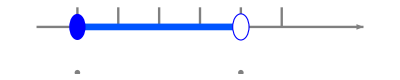

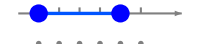

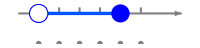

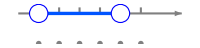

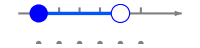

```mathematica
intervaloGE[a1_,b1_,paso_:1,tca_,aa_,bb_,tcb_,r_:0.1]:=
Graphics[{
AbsoluteThickness[1.7], Gray, Arrowheads[0.08],
Arrow[{{{a1-1,0}, {b1+2,0}}}],
Table[{Line[{{t,0},{t,0.3}}]},{t,a1,b1,paso}],
Text[MaTeX["a", Magnification->2],{0,-0.7}],
Text[MaTeX["b", Magnification->2],{4,-0.7}],
RGBColor[0, 0.333333, 1],Thickness[0.012],Line[{{aa,0},{bb,0}}],
Which[tca=="[",{Blue,Disk[{aa,0},r]},tca=="]",{EdgeForm[Directive[Thick,Blue]],White,Disk[{aa,0},r]}],
Which[tcb=="]", {Blue,Disk[{bb,0},r]},tcb=="[",{EdgeForm[Directive[Thick,Blue]],White,Disk[{bb,0},r]}]
}];
a=0; b=4;
intervaloGE[0,5,1, "[",a,b,"]",0.2]
intervaloGE[0,5,1, "]",a,b,"]",0.2]
intervaloGE[0,5,1, "]",a,b,"[",0.2]
intervaloGE[0,5,1, "[",a,b,"[",0.2]
```

## Interseccion Intervalos

{x==3,\{3\}}

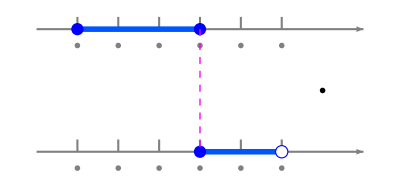

```mathematica
intervaloLT[a1_,b1_,paso_:1,ca_,aa_,cb_,bb_,tr_:3]:={
AbsoluteThickness[1.5], Gray, Arrowheads[0.08],
Arrow[{{{a1-1,-tr}, {b1+2,-tr}}}],
Table[{Line[{{t,-tr},{t,-tr+0.3}}]},{t,a1,b1,paso}],
Table[Text[MaTeX[t, Magnification->1.2],{t,-tr-0.4}],{t,a1,b1,paso}],
RGBColor[0, 0.333333, 1],Thickness[0.01],Line[{{aa,-tr},{bb,-tr}}],
Which[ca=="[",{Blue,Disk[{aa,-tr},0.15]},ca=="]",{EdgeForm[Directive[Thick,Blue]],White,Disk[{aa,-tr},0.15]}],
Which[cb=="]", {Blue,Disk[{bb,-tr},0.15]},cb=="[",{EdgeForm[Directive[Thick,Blue]],White,Disk[{bb,-tr},0.15]}]
};
(**)
lv[ts1_,aa3_,bb3_,ts2_,tr_,pr_]:=Module[{s},Which[aa3<bb3,
s={ 
Magenta,Thickness[0.01],Line[{{aa3,-tr/2},{bb3,-tr/2}}],
Which[ts1=="[",{Blue,Disk[{aa3,-tr/2},0.15]},ts1=="]",{EdgeForm[Directive[Thick,Blue]],White,Disk[{aa3,-tr/2},0.15]}],
Which[ts2=="]", {Blue,Disk[{bb3,-tr/2},0.15]},ts2=="[",{EdgeForm[Directive[Thick,Blue]],White,Disk[{bb3,-tr/2},0.15]}],
(*verticales*)
Thick, Dashed, Magenta, Line[{{aa3,0},{aa3,-tr}}],
 Line[{{bb3,0},{bb3,-tr}}]
},
aa3==bb3,s={Thick, Dashed, Magenta, Line[{{aa3,0},{aa3,-tr}}]}, 
aa3>bb3,{Thick, Dashed, Magenta, Line[{{pr,2},{pr,-tr-2}}]}
]; 
s
];
(**)
soluint[tca1_,aa1_,bb1_,tcb1_,tca2_,aa2_,bb2_,tcb2_,solu_,posd_,posal_]:={Text[MaTeX[tca1<>ToString[aa1]<>","<>ToString[bb1]<>tcb1
<>"\\,\\medcap\\,"
<> tca2<>ToString[aa2]<>","<>ToString[bb2]<>tcb2
<>"\\,=\\,"<> solu
,Magnification->1.6],{posd+1,-posal/2},{-1,0}]};
(**)
Graphics@soluint["[",0,7,"[","]",3,9,"]" ,"\\emptyset ",0];
(**)
traducir[expr_]:=Module[{s},
Which[expr=={Less,LessEqual},s={ "]",  "]"}]; 
Which[expr=={LessEqual,Less},s={ "[",  "["}];
Which[expr=={LessEqual,LessEqual},s={ "[",  "]"}];
Which[expr=={Less,Less},s={ "]",  "["}];
 s
                                                ];

(*Intersección de intervalos sin extremos infinitos*)
interseccion[desx1_,desx2_]:=Module[{solu,ls,tca1,aa1,bb1,tcb1,tca2,aa2,bb2,tcb2 ,tb,lasolu,ts1,ts2,min,max,pr,aa3,bb3},

Which[Head[desx1]==LessEqual, tca1="[";tcb1="]";{aa1,bb1}={desx1[[1]],desx1[[3]]}];
Which[ Head[desx1]==Less, tca1="]";tcb1="[";{aa1,bb1}={desx1[[1]],desx1[[3]]}];
Which[Head[desx2]==LessEqual, tca2="[";tcb2="]";{aa2,bb2}={desx2[[1]],desx2[[3]]}];
Which[ Head[desx2]==Less, tca2="]";tcb2="[";
{aa2,bb2}={desx2[[1]],desx2[[3]]}];
Which[Head[desx1]==Inequality, {tca1,tcb1}=traducir[{desx1[[2]],desx1[[4]]}];
{aa1,bb1}={desx1[[1]],desx1[[5]]}];
Which[Head[desx2]==Inequality, {tca2,tcb2}=traducir[{desx2[[2]],desx2[[4]]}];
{aa2,bb2}={desx2[[1]],desx2[[5]]}];
(*Extraer coeficientes*)
min=Min[{aa1,aa2,bb1,bb2}]; max=Max[{aa1,aa2,bb1,bb2}];
pr=Which[bb1≤aa2,(bb1+aa2)/2,bb2≤aa1,(bb2+aa1)/2];
(*Print[{Head[desx1],tca1,aa1,bb1,tcb1,tca2,aa2,bb2,tcb2}];*)
solu=Reduce[desx1&&desx2];
(*Casos*)
(*1. No solución*)
If[Length[solu]==0, lasolu="\\emptyset"; aa3=pr; bb3=pr];
(*1. Una solución*)
If[Head[solu]==Equal, lasolu="\\{"<>ToString[solu[[2]]]<>"\\}"; aa3=solu[[2]];bb3=solu[[2]] ];
(*2. Un intervalo*)
Which[Head[solu]==Inequality, {ts1,ts2}=traducir[{solu[[2]],solu[[4]]}]];
(*Print[{solu,Head[solu],traducir[{solu[[2]],solu[[4]]}]}];*)

If[Head[solu]==Inequality, 
lasolu=ts1<>ToString[solu[[1]]]<>","<>ToString[solu[[5]]]<>ts2;
aa3=solu[[1]]; bb3=solu[[5]]
];
Print[{solu,lasolu}];
Graphics[{
intervaloLT[min,max,1,tca1,aa1,tcb1,bb1,0],
intervaloLT[min,max,1,tca2,aa2,tcb2,bb2,3],
lv[ts1,aa3,bb3,ts2,3,pr],
soluint[tca1,aa1,bb1,tcb1,tca2,aa2,bb2,tcb2,lasolu,max,3]
}, ImageSize->400]

];
interseccion[0≤x<=3,3<=x<5]
```

```mathematica
s=Reduce[4<=x<10&&4<=x≤5];
{s,Head[s], Length[s], s[[3]]}
```

{4≤x≤5,Inequality,5,x}

```mathematica
exp=4≤x ≤4;
{Head[exp],expr[[1]],expr[[5]]}
```

{LessEqual,4,5}

## Geodesicas

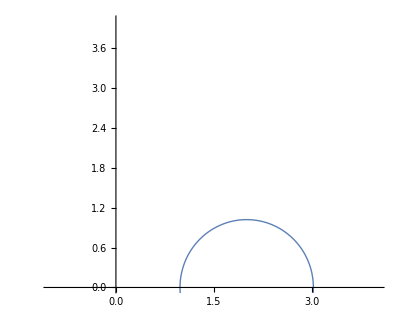

```mathematica
GeodesicaPoincare[P1_,P2_]:=Module[{x1,y1,x2,y2,center,radius,theta1,theta2},(*Coordenadas de los puntos*){x1,y1}=P1;
{x2,y2}=P2;
If[x1==x2,(*Caso especial:Línea vertical*)Plot[{x1},{y,Min[y1,y2],Max[y1,y2]},PlotStyle->Thick],(*Caso general:Circunferencia ortogonal al eje x*)center=(x1^2-x2^2+y1^2-y2^2)/(2 (x1-x2));
radius=Sqrt[(x1-center)^2+y1^2];
ParametricPlot[{center+radius Cos[t],radius Sin[t]},{t,-Pi,Pi},PlotRange->{{-1,4},{0,4}},Axes->True,AxesOrigin->{0,0},PlotStyle->Thick]]]

(*Ejemplo de uso:*)
GeodesicaPoincare[{1,0.2},{3,0.2}]
```

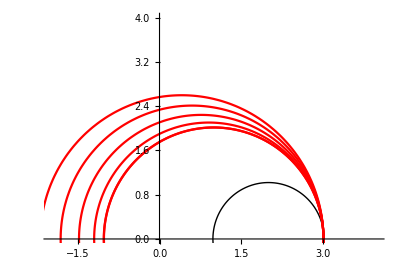

```mathematica
GeodesicasPoincare[P1_,P2_,P3_,n_]:=Module[{x1,y1,x2,y2,x3,y3,center,radius,mainGeodesic,parallels,delta},(*Coordenadas de los puntos*){x1,y1}=P1;
{x2,y2}=P2;
{x3,y3}=P3;
(*Calcular el centro y radio de la circunferencia ortogonal al eje x que pasa por P1 y P2*)center=(x1^2-x2^2+y1^2-y2^2)/(2 (x1-x2));
radius=Sqrt[(x1-center)^2+y1^2];
(*Geodésica principal:Negra y gruesa*)mainGeodesic=ParametricPlot[{center+radius Cos[t],radius Sin[t]},{t,-Pi,Pi},PlotStyle->{Thick,Black}];
(*Generar las geodésicas paralelas que pasan por P3*)delta=0.5;(*Separación entre geodésicas paralelas*)parallels=Table[Module[{newP1,newCenter,newRadius},newP1={x3+k delta,y3};
newCenter=(newP1[[1]]^2-x2^2+newP1[[2]]^2-y2^2)/(2 (newP1[[1]]-x2));
newRadius=Sqrt[(newP1[[1]]-newCenter)^2+newP1[[2]]^2];
ParametricPlot[{newCenter+newRadius Cos[t],newRadius Sin[t]},{t,-Pi,Pi},PlotStyle->{Red}]],{k,-n/2,n/2}];
(*Mostrar todas las geodésicas juntas*)Show[{mainGeodesic,parallels},PlotRange->{{-2,4},{0,4}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic]]

(*Ejemplo de uso*)
GeodesicasPoincare[{1,0.2},{3,0.2},{0,2},5]
```

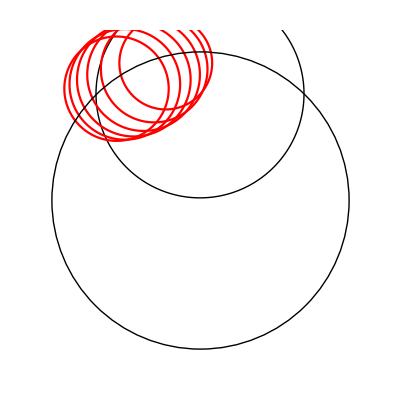

```mathematica
GeodesicasPoincareDisco[P1_,P2_,P3_,n_]:=Module[{z1,z2,z3,mainGeodesic,parallels,delta,CircleFromPoints},(*Función para hallar centro y radio de la circunferencia que pasa por dos puntos en el disco*)CircleFromPoints[p1_,p2_]:=Module[{m,c,r},If[Norm[p1]==1||Norm[p2]==1,Return[{}]];(*Los puntos deben estar dentro del disco*)If[p1===-p2,(*Si son opuestos,la geodésica es un diámetro*){0,0},(*Centro del disco*)(*Caso general:cálculo del círculo ortogonal al borde*)c=(p1+p2)/(1+p1.p2);
r=Sqrt[Norm[c]^2-1];
{c,Abs[r]}]];
(*Geodésica principal entre P1 y P2*){z1,z2}={P1,P2};
{mainCenter,mainRadius}=CircleFromPoints[z1,z2];
mainGeodesic=If[mainCenter==={0,0},(*Si es un diámetro*)Line[{P1,P2}],(*Si es un arco de circunferencia*)ParametricPlot[mainCenter+mainRadius {Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->{Thick,Black}]];
(*Generar geodésicas paralelas que pasan por P3*)delta=0.1;(*Separación entre geodésicas paralelas*)z3=P3;
parallels=Table[Module[{newP1,newCenter,newRadius},newP1={P3[[1]]+k delta,P3[[2]]};
{newCenter,newRadius}=CircleFromPoints[newP1,P2];
If[newCenter==={},Nothing,If[newCenter==={0,0},Line[{newP1,P2}],ParametricPlot[newCenter+newRadius {Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->{Red}]]]],{k,-n/2,n/2}];
(*Mostrar todas las geodésicas juntas en el disco*)Show[{mainGeodesic,parallels,Graphics[{Circle[{0,0},1]}]},PlotRange->{{-1.1,1.1},{-1.1,1.1}},Axes->False,AspectRatio->1]]

(*Ejemplo de uso:*)
GeodesicasPoincareDisco[{0.5,0.3},{-0.5,0.3},{0,0.7},5]
```

```mathematica
(*Distancia en el Disco de Poincaré*)poincareMetric[u_?VectorQ,v_?VectorQ]:=Abs[ArcCosh[1+2 SquaredEuclideanDistance[u,v]/((1-u.u) (1-v.v))]]

(*Geodésica entre dos puntos usando NURBS en el Disco de Poincaré*)
poincareLine[{p1_,p2_}]:=Module[{s=p1.p2-1,tm=Transpose[{p2,p1}]},BSplineCurve[{p1,tm.({p1.p1,p2.p2}-1)/(2 s),p2},SplineDegree->2,SplineKnots->{0,0,0,1,1,1},SplineWeights->{1,1/Sqrt[1+(Det[tm]/s)^2],1}]]

(*Función principal para dibujar la geodésica principal y sus paralelas*)
GeodesicasPoincareDisco[P1_,P2_,P3_,n_]:=Module[{mainGeodesic,parallels,delta},(*Geodésica principal en negro grueso*)mainGeodesic=Graphics[{Thick,Black,poincareLine[{P1,P2}]}];
(*Generar geodésicas paralelas que pasan por P3*)delta=0.1;(*Separación entre geodésicas paralelas*)parallels=Table[Module[{newP1},newP1={P3[[1]]+k delta,P3[[2]]};
Graphics[{Red,poincareLine[{newP1,P2}]}]],{k,-n/2,n/2}];
(*Mostrar todo en el disco de Poincaré*)Show[{mainGeodesic,parallels,Graphics[{Circle[{0,0},1]}]},PlotRange->All,Axes->False,AspectRatio->1]]

(*Ejemplo de uso*)
GeodesicasPoincareDisco[{0.5,0.3},{-0.5,0.3},{0,0.7},5]
```

-Graphics-

```mathematica
poincareMetric[u_?VectorQ,v_?VectorQ]:=Abs[ArcCosh[1+2 SquaredEuclideanDistance[u,v]/((1-u.u) (1-v.v))]]

(*NURBS representation of a line on the Poincaré disk*)
poincareLine[{p1_,p2_}]:=Module[{s=p1.p2-1,tm=Transpose[{p2,p1}]},BSplineCurve[{p1,tm.({p1.p1,p2.p2}-1)/(2 s),p2},SplineDegree->2,SplineKnots->{0,0,0,1,1,1},SplineWeights->{1,1/Sqrt[1+(Det[tm]/s)^2],1}]]

With[{n=20(*number of points*),r=3,(*hyperbolic radius of disk*)h=0.35 (*fraction of radius to consider drawing an edge*)},BlockRandom[SeedRandom[42,Method->"MersenneTwister"];(*for reproducibility*)pts=Table[With[{t=RandomReal[]},(*hint:derive the inverse CDF*)Sqrt[(t Sinh[r/2]^2)/(1+t Sinh[r/2]^2)]] Normalize[RandomVariate[NormalDistribution[],2]],{n}]];
NearestNeighborGraph[pts,{All,h r},DistanceFunction->poincareMetric,EdgeShapeFunction->(poincareLine[#1]&),PlotRange->All,Prolog->{Directive[Opacity[1/2],AbsoluteThickness[1]],Circle[]}]]
```

-Graphics-

```mathematica
(*Distancia en el Disco de Poincaré*)poincareMetric[u_?VectorQ,v_?VectorQ]:=Abs[ArcCosh[1+2 SquaredEuclideanDistance[u,v]/((1-u.u) (1-v.v))]]

(*Geodésica entre dos puntos usando NURBS en el Disco de Poincaré*)
poincareLine[{p1_,p2_}]:=Module[{s=p1.p2-1,tm=Transpose[{p2,p1}],extendedP1,extendedP2},(*Extender puntos hasta el borde del disco*)extendedP1=p1/Norm[p1];
extendedP2=p2/Norm[p2];
BSplineCurve[{extendedP1,tm.({extendedP1.extendedP1,extendedP2.extendedP2}-1)/(2 s),extendedP2},SplineDegree->2,SplineKnots->{0,0,0,1,1,1},SplineWeights->{1,1/Sqrt[1+(Det[tm]/s)^2],1}]]

(*Función principal para dibujar la geodésica principal y sus paralelas*)
GeodesicasPoincareDisco[P1_,P2_,P3_,n_]:=Module[{mainGeodesic,parallels,delta},(*Geodésica principal en negro grueso*)mainGeodesic=Graphics[{Thick,Black,poincareLine[{P1,P2}]}];
(*Generar geodésicas paralelas que pasan por P3*)delta=0.1;(*Separación entre geodésicas paralelas*)parallels=Table[Module[{newP1},newP1={P3[[1]]+k delta,P3[[2]]};
Graphics[{Red,poincareLine[{newP1,P2}]}]],{k,-n/2,n/2}];
(*Mostrar todo en el disco de Poincaré*)Show[{mainGeodesic,parallels,Graphics[{Circle[{0,0},1]}]},PlotRange->{{-1.1,1.1},{-1.1,1.1}},Axes->False,AspectRatio->1]]

(*Ejemplo de uso*)
GeodesicasPoincareDisco[{0.5,-0.3},{-0.5,-0.3},{0,0.7},5]
```

-Graphics-

```mathematica
(*Distancia en el Disco de Poincaré*)poincareMetric[u_?VectorQ,v_?VectorQ]:=Abs[ArcCosh[1+2 SquaredEuclideanDistance[u,v]/((1-u.u) (1-v.v))]]

(*Geodésica entre dos puntos usando NURBS en el Disco de Poincaré*)
poincareLine[{p1_,p2_}]:=Module[{s=p1.p2-1,tm=Transpose[{p2,p1}],extendedP1,extendedP2},(*Extender puntos hasta el borde del disco*)extendedP1=p1/Norm[p1];
extendedP2=p2/Norm[p2];
BSplineCurve[{extendedP1,tm.({extendedP1.extendedP1,extendedP2.extendedP2}-1)/(2 s),extendedP2},SplineDegree->2,SplineKnots->{0,0,0,1,1,1},SplineWeights->{1,1/Sqrt[1+(Det[tm]/s)^2],1}]]

(*Generar un punto paralelo a P3 en el disco de Poincaré*)
ParallelPoint[P3_,k_,delta_]:=Module[{angle,newP},angle=ArcTan[P3[[2]],P3[[1]]]+k delta;
newP={Cos[angle],Sin[angle]}*Norm[P3];(*Mantiene la distancia hiperbólica*)newP]

(*Función principal para dibujar la geodésica principal y sus paralelas*)
GeodesicasPoincareDisco[P1_,P2_,P3_,n_]:=Module[{mainGeodesic,parallels,delta},(*Geodésica principal en negro grueso*)mainGeodesic=Graphics[{Thick,Black,poincareLine[{P1,P2}]}];
(*Generar geodésicas paralelas que pasan por P3*)delta=0.2;(*Separación angular entre geodésicas paralelas*)parallels=Table[Module[{newP1},newP1=ParallelPoint[P3,k,delta];
Graphics[{Red,poincareLine[{newP1,P2}]}]],{k,-n/2,n/2}];
(*Mostrar todo en el disco de Poincaré*)Show[{mainGeodesic,parallels,Graphics[{Circle[{0,0},1]}]},PlotRange->{{-1.1,1.1},{-1.1,1.1}},Axes->False,AspectRatio->1]]

(*Ejemplo de uso*)
GeodesicasPoincareDisco[{0.5,0.3},{-0.5,0.3},{0,0.7},5]
```

-Graphics-

```mathematica
(*Distancia en el Disco de Poincaré*)poincareMetric[u_?VectorQ,v_?VectorQ]:=Abs[ArcCosh[1+2 SquaredEuclideanDistance[u,v]/((1-u.u) (1-v.v))]]

(*Geodésica entre dos puntos usando NURBS en el Disco de Poincaré*)
poincareLine[{p1_,p2_}]:=Module[{s=p1.p2-1,tm=Transpose[{p2,p1}],extendedP1,extendedP2},(*Extender puntos hasta el borde del disco*)extendedP1=p1/Norm[p1];
extendedP2=p2/Norm[p2];
BSplineCurve[{extendedP1,tm.({extendedP1.extendedP1,extendedP2.extendedP2}-1)/(2 s),extendedP2},SplineDegree->2,SplineKnots->{0,0,0,1,1,1},SplineWeights->{1,1/Sqrt[1+(Det[tm]/s)^2],1}]]

(*Función para dibujar un punto grande y negro*)
drawPoint[p_]:=Graphics[{Black,PointSize[Large],Point[p]}]

(*Generar geodésicas paralelas basadas en traslaciones hiperbólicas*)
poincareParallel[{p3_,p2_},angle_]:=Module[{rotatedP3},rotatedP3=RotationTransform[angle][p3];
poincareLine[{rotatedP3,p2}]]

(*Función principal para dibujar la geodésica principal y sus paralelas*)
GeodesicasPoincareDisco[P1_,P2_,P3_,n_]:=Module[{mainGeodesic,parallels,delta,angle},(*Geodésica principal en negro grueso*)mainGeodesic=Graphics[{Thick,Black,poincareLine[{P1,P2}]}];
(*Dibujar los puntos P1,P2 y P3*)points={drawPoint[P1],drawPoint[P2],drawPoint[P3]};
(*Generar geodésicas paralelas que pasan por P3*)delta=Pi/12;(*Separación angular entre geodésicas paralelas*)parallels=Table[Module[{parallel},parallel=poincareParallel[{P3,P2},k delta];
Graphics[{Red,parallel}]],{k,-n/2,n/2}];
(*Mostrar todo en el disco de Poincaré*)Show[{mainGeodesic,parallels,Graphics[{Circle[{0,0},1]}],points},PlotRange->{{-1.1,1.1},{-1.1,1.1}},Axes->False,AspectRatio->1]]

(*Ejemplo de uso*)
GeodesicasPoincareDisco[{0.5,0.3},{-0.5,0.3},{0,0.7},5]
```

-Graphics-

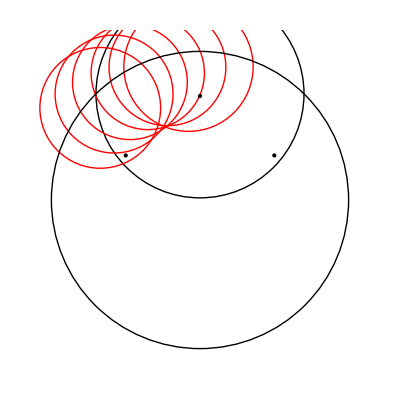

```mathematica
(*Distancia en el Disco de Poincaré*)poincareMetric[u_?VectorQ,v_?VectorQ]:=Abs[ArcCosh[1+2 SquaredEuclideanDistance[u,v]/((1-u.u) (1-v.v))]]

(*Geodésica entre dos puntos usando NURBS en el Disco de Poincaré*)
poincareLine[{p1_,p2_}]:=Module[{s=p1.p2-1,tm=Transpose[{p2,p1}],extendedP1,extendedP2},(*Extender puntos hasta el borde del disco*)extendedP1=p1/Norm[p1];
extendedP2=p2/Norm[p2];
BSplineCurve[{extendedP1,tm.({extendedP1.extendedP1,extendedP2.extendedP2}-1)/(2 s),extendedP2},SplineDegree->2,SplineKnots->{0,0,0,1,1,1},SplineWeights->{1,1/Sqrt[1+(Det[tm]/s)^2],1}]]

(*Función para dibujar un punto grande y negro*)
drawPoint[p_]:=Graphics[{Black,PointSize[Large],Point[p]}]

(*Calcular centro y radio de la circunferencia ortogonal que pasa por dos puntos*)
calculateCircle[{p1_,p2_}]:=Module[{m,c,r},If[Norm[p1]==1||Norm[p2]==1,Return[{}]];
c=(p1+p2)/(1+p1.p2);
r=Sqrt[Norm[c]^2-1];
{c,Abs[r]}]

(*Dibujar circunferencia de geodésica*)
drawGeodesic[{p1_,p2_},color_]:=Module[{c,r},{c,r}=calculateCircle[{p1,p2}];
If[c==={},Return[{}]];
Graphics[{color,Thick,Circle[c,r]}]]

(*Generar geodésicas paralelas basadas en P3*)
generateParallel[{p3_,p2_},angle_]:=Module[{c,r,rotatedP3},rotatedP3=RotationTransform[angle][p3];
drawGeodesic[{rotatedP3,p2},Red]]

(*Función principal para dibujar la geodésica principal y sus paralelas*)
GeodesicasPoincareDisco[P1_,P2_,P3_,n_]:=Module[{mainGeodesic,parallels,delta,angle,points},(*Geodésica principal en negro que pasa por P1 y P2*)mainGeodesic=drawGeodesic[{P1,P2},Black];
(*Dibujar los puntos P1,P2 y P3*)points={drawPoint[P1],drawPoint[P2],drawPoint[P3]};
(*Generar geodésicas paralelas que pasan por P3*)delta=Pi/12;(*Separación angular entre geodésicas paralelas*)parallels=Table[Module[{parallel},parallel=generateParallel[{P3,P2},k delta];
parallel],{k,-n/2,n/2}];
(*Mostrar todo en el disco de Poincaré*)Show[{mainGeodesic,parallels,Graphics[{Circle[{0,0},1]}],points},PlotRange->{{-1.1,1.1},{-1.1,1.1}},Axes->False,AspectRatio->1]]

(*Ejemplo de uso*)
GeodesicasPoincareDisco[{0.5,0.3},{-0.5,0.3},{0,0.7},5]
```